## IntertiaMatrix-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51d (10 June 2017)) loaded Sat 10 Jun 2017 17:43:38
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

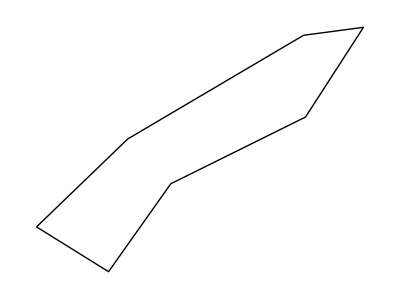

```mathematica
polygon={{0.6656821861024209,0.5885139068629628},{0.3674265409089722,0.548792012192189},{-0.5083022778120968,0.03200749861905844},{-0.9625187848327785,-0.40634552703524995},{-0.603944818863048,-0.6296344493677282},{-0.2938861906733466,-0.19134629851828722},{0.3771323695082593,0.14124017268253336}};
Boundary[polygon]
```

```mathematica
InertiaMatrix[polygon]
```

{{0.110189,0.0605324},{0.0605324,0.0490591}}

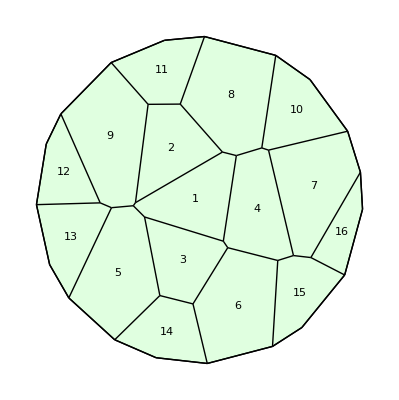

```mathematica
w=TemplateRandomCircularGrid[16,100];
ShowTissue[w, "CellNumbers"-> True]
```

```mathematica
MatrixForm[InertiaMatrix[w,3]]
```

(395038. | 592119.
592119. | 2.40048×10^6)

```mathematica
MatrixForm/@InertiaMatrix[w]
```

{(424388. | 86749.3
86749.3 | 275021.),(790334. | 930981.
930981. | 2.15512×10^6),(395038. | 592119.
592119. | 2.40048×10^6),(2.62687×10^6 | 458356.
458356. | 703470.),(7.27978×10^6 | 6.29033×10^6
6.29033×10^6 | 6.55215×10^6),(1.92248×10^6 | 3.97163×10^6
3.97163×10^6 | 1.21538×10^7),(1.33847×10^7 | 1.67234×10^6
1.67234×10^6 | 1.09764×10^6),(1.59919×10^6 | 3.54062×10^6
3.54062×10^6 | 1.30745×10^7),(9.41574×10^6 | 6.4931×10^6
6.4931×10^6 | 5.86572×10^6),(6.08926×10^6 | 5.37991×10^6
5.37991×10^6 | 5.27909×10^6),(1.00512×10^6 | 2.64516×10^6
2.64516×10^6 | 9.31926×10^6),(8.24814×10^6 | 1.71164×10^6
1.71164×10^6 | 558863.),(9.40001×10^6 | 2.68855×10^6
2.68855×10^6 | 1.04997×10^6),(810319. | 2.3192×10^6
2.3192×10^6 | 9.50165×10^6),(5.37702×10^6 | 4.75143×10^6
4.75143×10^6 | 4.6702×10^6),(6.50391×10^6 | 1.39691×10^6
1.39691×10^6 | 496112.)}